```mathematica
(* zadacha 1 *)
```

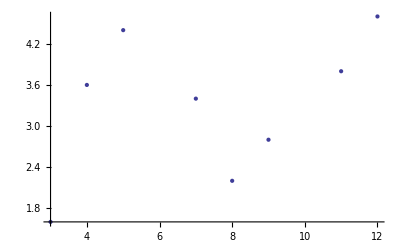

```mathematica
xs = {3,4,5,7,8,9,11,12};
ys = {1.6,3.6,4.4,3.4,2.2,2.8,3.8,4.6};
dots = {};
For[i=1,i<=Length[xs],i++,
AppendTo[dots,{xs[[i]],ys[[i]]}]
];
listDots = ListPlot[dots]
```

-11.4887+7.14382 x-1.04121 x^2+0.046676 x^3

-27.2372+17.8734 x-3.55442 x^2+0.289185 x^3-0.00822284 x^4

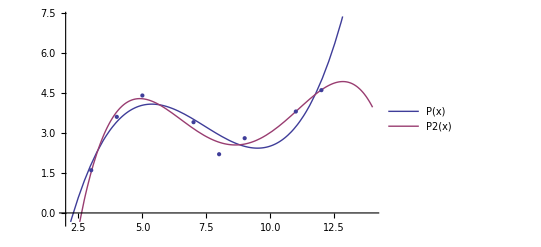

```mathematica
P[x_] = -b*x^3 + c*x^2 -d*x + e;
P2[x_] =a2*x^4 -b2*x^3 + c2*x^2 -d2*x + e2;
sum = ∑_(i=1)^Length[xs] (P[xs[[i]]] - ys[[i]])^2;
sum2 = ∑_(i=1)^Length[xs] (P2[xs[[i]]] - ys[[i]])^2;
coeffs = NSolve[{D[sum, b] ==0,D[sum, c] ==0,D[sum, d] ==0,D[sum, e] ==0},{b,c,d,e}];
coeffs2 = NSolve[{D[sum2, b2] ==0,D[sum2, a2] ==0,D[sum2, c2] ==0,D[sum2, d2] ==0,D[sum2, e2] ==0 },{b2,c2,d2,e2,a2}];

P[x_] = P[x]/.coeffs[[1]]
P2[x_] = P2[x]/.coeffs2[[1]]
plot = Plot[{P[x],P2[x]},{x,2,xs[[Length[xs]]]+2}  ,PlotLegends->"Expressions"];
Show[plot,listDots]
```

```mathematica
(* Тъй като се колебая точно кой полином трябва да се вземе, ще взема под предвид,че полиномът от 4та степен се допира до повече точки и е на почти еднакво разстояние от другите *)
```

-27.2372+17.8734 x-3.55442 x^2+0.289185 x^3-0.00822284 x^4

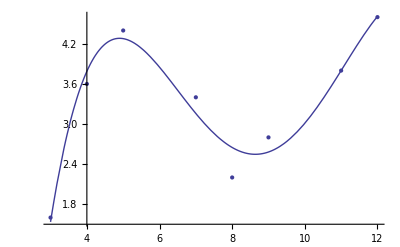

```mathematica
P2[x]
Show[Plot[{P2[x]},{x,xs[[1]],xs[[Length[xs]]]},PlotRange->All] ,listDots ]
```

```mathematica
(* zadacha 2 *)
(* Моля Ви, ако използвате Quit Kernel след всяка задача, да го направите 2 пъти подред за тази преди да я разглеждате. *)
```

(3 π)/2

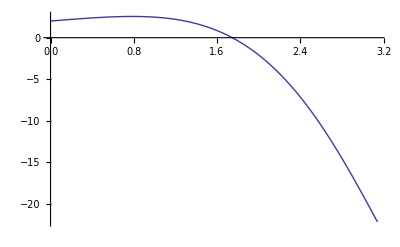

(3 π)/2

```mathematica
Trapezoids[f_,a_,b_,ϵ_] :=(
func = f;
F[x_] = func;

R[ksi_] = -F''[ksi]/12*(b-a)^3 ;

wrong=0;
If[R[a]>R[b],
wrong = R[a] //Abs,
wrong = R[b] //Abs
];

h = (b-a)/(2n);

xses = {};
For[ i =0,i<=n,i++,
AppendTo[xses,a+i*h];
];

n = Round[√(wrong/Abs[ϵ])]+1;
sum = 0;
For[i=2,i<=n+1,i++,
sum += F[xses[[i-1]]] + F[xses[[i]]]
];
integral = h*sum;

Print[integral];
(* Graphics *)
plotFunction = Plot[F[x],{x,a,b}];
Print[Show[plotFunction]];


integral
)
Trapezoids[1+E^x*Cos[x],0,π,5]
```

```mathematica
(* zadacha 3 *)
```

```mathematica
w = √(1-x^2);
oldCoef[k_] = 2^k;
Subscript[P, 0] = oldCoef[0];
Subscript[P, 1] = oldCoef[1] *x +a;
Subscript[P, 2] = oldCoef[2]*x^2+b*x +c;
```

```mathematica
coefs = Solve[{
 ∫_-1^1 w*Subscript[P, 0]*Subscript[P, 1] ⅆx == 0,
 ∫_-1^1 w*Subscript[P, 0]*Subscript[P, 2] ⅆx == 0,
 ∫_-1^1 w*Subscript[P, 2]*Subscript[P, 1] ⅆx == 0
},{a,b,c}]
```

{{a→0,b→0,c→-1}}

```mathematica
Subscript[P, 0]
Subscript[P, 1]= Subscript[P, 1]/.coefs[[1]]
Subscript[P, 2] = Subscript[P, 2] /.coefs[[1]]
```

1

2 x

-1+4 x^2